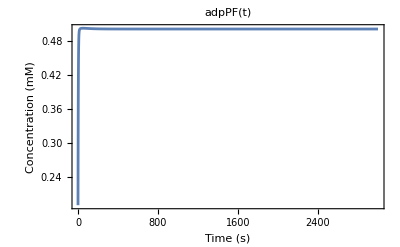
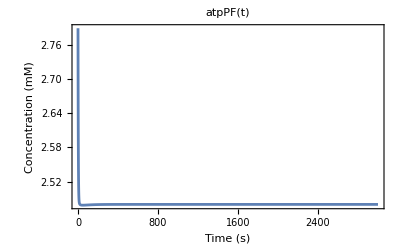
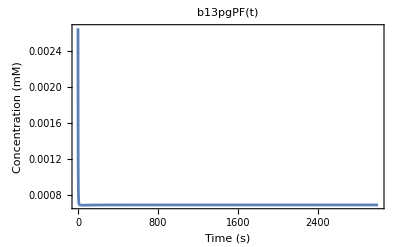
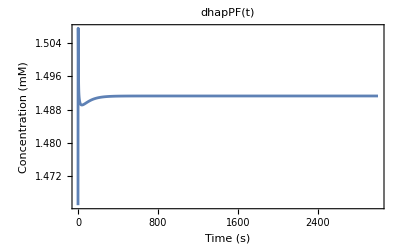
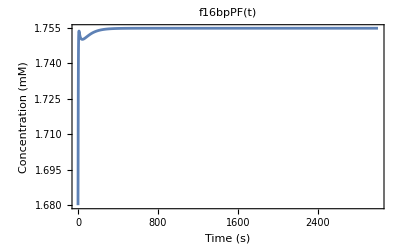
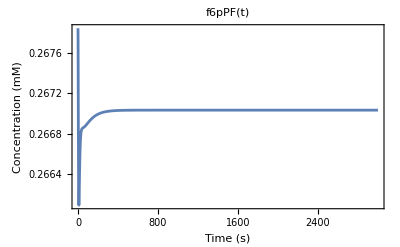
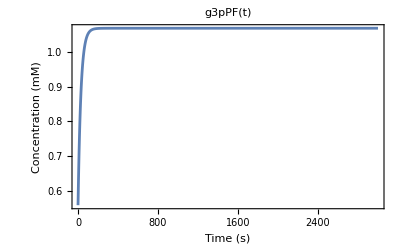
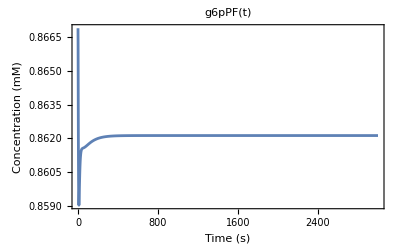

```mathematica
(*Merged models in SI units*)

variables={
(*vanniekerk1 model*)
adpPF[t],atpPF[t],b13pgPF[t],dhapPF[t],f16bpPF[t],f6pPF[t],g3pPF[t],g6pPF[t],gapPF[t],glcPF[t],lacPF[t],nadhPF[t],nadPF[t],p2gPF[t],p3gPF[t],pepPF[t],pyrPF[t],

(*IRIP model*)
Nap[t], Kp[t], Clp[t], pHp[t], p[t], Ep[t], Yp[t]
};

initialValues={
(*Initial values (steady state values of vanniekerk1) in mM*)
adpPF[0]==0.191,atpPF[0]==2.789,b13pgPF[0]==0.002678,dhapPF[0]==1.465,f16bpPF[0]==1.680,f6pPF[0]==0.26785,g3pPF[0]==0.55852,g6pPF[0]==0.8669,gapPF[0]==0.06228,glcPF[0]==0.71055,lacPF[0]==3.558,nadhPF[0]==0.05708,nadPF[0]==2.921,p2gPF[0]==0.061,p3gPF[0]==0.5789,pepPF[0]==0.0983,pyrPF[0]==1.3045,

(*Initial values (steady state values of IRIP) in mM*)
Nap[0]==10.019605515415787,Kp[0]==129.96155318019612,Clp[0]==69.94469672116819,pHp[0]==7.299865635766711,p[0]==27.023876030892215,Ep[0]==-0.09499137536042568,Yp[0]==116.86824231515405
};

rates={
(*rates vanniekerk1*)
vPFvALD,vPFvATPASE,vPFvENO,vPFvG3PDH,vPFvGAPDH,vPFvGLCtr,vPFvGLYtr,vPFvHK,vPFvLACtr,vPFvLDH,vPFvPFK,vPFvPGI,vPFvPGK,vPFvPGM,vPFvPK,vPFvPYRtr,vPFvTPI,

(*rates IRIP*)
v1,v2,v3,v4,naPRate,kPRate,clPRate,atpaseprate
};

rateEquations=
(*rate equations vanniekerk1 in mM/s*){vPFvALD->(1/60((VPFvALD*f16bpPF[t]*(1-(dhapPF[t]*gapPF[t])/(KeqPFvALD*Vpf*f16bpPF[t])))/(Kf16bpPFvALD*(1+dhapPF[t]/(KdhapPFvALD*Vpf)+f16bpPF[t]/(Kf16bpPFvALD*Vpf)+gapPF[t]/(KgapPFvALD*Vpf)+(dhapPF[t]*gapPF[t])/(KdhapPFvALD*KgapPFvALD*Vpf^2)))))*Ap/(p[t]*1*10^(-6)),vPFvATPASE->(1/60((VPFvATPASE*atpPF[t]^5)/(KmPFvATPASE^5*Vpf^4*(1+atpPF[t]^5/(KmPFvATPASE^5*Vpf^5)))))*Ap/(p[t]*1*10^(-6)),vPFvENO->(1/60((VPFvENO*p2gPF[t]*(1-pepPF[t]/(KeqPFvENO*p2gPF[t])))/(Kp2gPFvENO*(1+p2gPF[t]/(Kp2gPFvENO*Vpf)+pepPF[t]/(KpepPFvENO*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvG3PDH->(1/60((VfPFvG3PDH*dhapPF[t]*nadhPF[t]*(1-(g3pPF[t]*nadPF[t])/(KeqPFvG3PDH*dhapPF[t]*nadhPF[t])))/(KdhapPFvG3PDH*KnadhPFvG3PDH*Vpf*(1+dhapPF[t]/(KdhapPFvG3PDH*Vpf)+g3pPF[t]/(Kg3pPFvG3PDH*Vpf))*(1+nadhPF[t]/(KnadhPFvG3PDH*Vpf)+nadPF[t]/(KnadPFvG3PDH*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvGAPDH->(1/60((-((VrPFvGAPDH*b13pgPF[t]*nadhPF[t])/(Kb13pgPFvGAPDH*KnadhPFvGAPDH*Vpf))+(VPFvGAPDH*gapPF[t]*nadPF[t])/(KgapPFvGAPDH*KnadPFvGAPDH*Vpf))/((1+b13pgPF[t]/(Kb13pgPFvGAPDH*Vpf)+gapPF[t]/(KgapPFvGAPDH*Vpf))*(1+nadhPF[t]/(KnadhPFvGAPDH*Vpf)+nadPF[t]/(KnadPFvGAPDH*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvGLCtr->(1/60(((glcEX*Vpf*VPFvGLCtr)/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)-(VPFvGLCtr*glcPF[t])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr))/(1+(glcEX*(1+cytb/Ki2CytGlcTr))/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vex)+((1+cytb/Ki2CytGlcTr)*glcPF[t])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr*Vpf)+(alphaPFvGLCtr*glcEX*glcPF[t])/((1+cytb/Ki1CytGlcTr)*KPFvGLCtr^2*Vex*Vpf))))*Ap/(p[t]*1*10^(-6)),
vPFvGLYtr->(1/60(kPFvGLYtr*Vpf*(-(glyEX/Vex)+g3pPF[t]/Vpf)))Ap/(p[t]*1*10^(-6)),vPFvHK->(1/60((VPFvHK*atpPF[t]*(1-(adpPF[t]*g6pPF[t])/(KeqPFvHK*atpPF[t]*glcPF[t]))*glcPF[t])/(KatpPFvHK*KglcPFvHK*Vpf*(1+adpPF[t]/(KadpPFvHK*Vpf)+atpPF[t]/(KatpPFvHK*Vpf))*(1+atpPF[t]/(KiatpPFvHK*Vpf))*(1+g6pPF[t]/(Kg6pPFvHK*Vpf)+glcPF[t]/(KglcPFvHK*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvLACtr->(1/60(KdPFvLACtr*(Ap/(p[t]*1*10^(-6)))*(1-(pHConversionFactor/10^phEX*lacEX*Vpf)/(hPF*Vex*lacPF[t]))*lacPF[t]+(VPFvLACtr*(1-(pHConversionFactor/10^phEX*lacEX*Vpf)/(hPF*Vex*lacPF[t]))*lacPF[t])/(KlacPFvLACtr*(1+lacEX/(KlacPFvLACtr*Vex)+pyrEX/(KipyrPFvLACtr*Vex)+lacPF[t]/(KlacPFvLACtr*Vpf)+pyrPF[t]/(KipyrPFvLACtr*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvLDH->(1/60((-((VrPFvLDH*lacPF[t]*nadPF[t])/(KlacPFvLDH*KnadPFvLDH*Vpf))+(VfPFvLDH*nadhPF[t]*pyrPF[t])/(KnadhPFvLDH*KpyrPFvLDH*Vpf))/((1+nadhPF[t]/(KnadhPFvLDH*Vpf)+nadPF[t]/(KnadPFvLDH*Vpf))*(1+lacPF[t]/(KlacPFvLDH*Vpf)+pyrPF[t]/(KpyrPFvLDH*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvPFK->(1/60((VPFvPFK*atpPF[t]*f6pPF[t])/(KatpPFvPFK*Kf6pPFvPFK*Vpf*(1+atpPF[t]/(KatpPFvPFK*Vpf))*(1+adpPF[t]/(KadpPFvPFK*Vpf)+atpPF[t]/(KatpPFvPFK*Vpf))*(1+f16bpPF[t]/(Kf16bpPFvPFK*Vpf)+f6pPF[t]/(Kf6pPFvPFK*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvPGI->(1/60((VPFvPGI*(1-f6pPF[t]/(KeqPFvPGI*g6pPF[t]))*g6pPF[t])/(Kg6pPFvPGI*(1+f6pPF[t]/(Kf6pPFvPGI*Vpf)+g6pPF[t]/(Kg6pPFvPGI*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvPGK->(1/60((KadpPFvPGK*Kb13pgPFvPGK*KeqPFvPGK*VrPFvPGK*atpPF[t]*(-1+(KeqPFvPGK*adpPF[t]*b13pgPF[t])/(atpPF[t]*p3gPF[t]))*p3gPF[t])/(KatpPFvPGK^2*Kp3gPFvPGK^2*Vpf*(1+adpPF[t]/(KadpPFvPGK*Vpf)+atpPF[t]/(KatpPFvPGK*Vpf))*(1+b13pgPF[t]/(Kb13pgPFvPGK*Vpf)+p3gPF[t]/(Kp3gPFvPGK*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvPGM->(1/60((VPFvPGM*(1-p2gPF[t]/(KeqPFvPGM*p3gPF[t]))*p3gPF[t])/(Kp3gPFvPGM*(1+p2gPF[t]/(Kp2gPFvPGM*Vpf)+p3gPF[t]/(Kp3gPFvPGM*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvPK->(1/60((VPFvPK*adpPF[t]*pepPF[t])/(KadpPFvPK*KpepPFvPK*Vpf*(1+adpPF[t]/(KadpPFvPK*Vpf))*(1+pepPF[t]/(KpepPFvPK*Vpf))*(1+LPFvPK*(1+(adpPF[t]/(KiadpPFvPK*Vpf)+atpPF[t]/(KiatpPFvPK*Vpf))^h)*(1+(pepPF[t]/(KipepPFvPK*Vpf)+pyrPF[t]/(KipyrPFvPK*Vpf))^h)))))*Ap/(p[t]*1*10^(-6)),vPFvPYRtr->(1/60(KdPFvPYRtr*(Ap/(p[t]*1*10^(-6)))*(1-(pHConversionFactor/10^phEX*pyrEX*Vpf)/(hPF*Vex*pyrPF[t]))*pyrPF[t]+(VPFvPYRtr*(1-(pHConversionFactor/10^phEX*pyrEX*Vpf)/(hPF*Vex*pyrPF[t]))*pyrPF[t])/(KpyrPFvPYRtr*(1+lacEX/(KilacPFvPYRtr*Vex)+pyrEX/(KpyrPFvPYRtr*Vex)+lacPF[t]/(KilacPFvPYRtr*Vpf)+pyrPF[t]/(KpyrPFvPYRtr*Vpf)))))*Ap/(p[t]*1*10^(-6)),vPFvTPI->(1/60((VPFvTPI*dhapPF[t]*(1-gapPF[t]/(KeqPFvTPI*dhapPF[t])))/(KdhapPFvTPI*(1+dhapPF[t]/(KdhapPFvTPI*Vpf)+gapPF[t]/(KgapPFvTPI*Vpf)+pepPF[t]/(KipepPFvTPI*Vpf)))))*Ap/(p[t]*1*10^(-6)),

(*rate equations IRIP in mM/s*)
v1-> dVp,
v2->-(sPfATP4H*JPfATP4salp*Ap/(p[t]*1*10^(-6))-sVtypeH*JVtypesalp*Ap/(p[t]*1*10^(-6))-sPfHClH*JPfHClsalp*Ap/(p[t]*1*10^(-6))-ghkfluxHsalp*Ap/(p[t]*1*10^(-6)))/bp,
v3-> (-F/Cm)*(sVtypeH*JVtypesalp+JPfKchannelsalp+(sPfATP4Na-sPfATP4H)*JPfATP4salp+(sPfHClH-sPfHClCl)*JPfHClsalp+zH*ghkfluxHsalp+zNa*ghkfluxNasalp+zK*ghkfluxKsalp+zCl*ghkfluxClsalp),
v4-> 0-Yp[t]*dVp/p[t],
naPRate-> (sPfATP4Na*JPfATP4salp+ghkfluxNasalp)*Ap/(p[t]*1*10^(-6)),
kPRate-> (1*JPfKchannelsalp+ghkfluxKsalp)*Ap/(p[t]*1*10^(-6)),
clPRate-> (sPfHClCl*JPfHClsalp+ghkfluxClsalp)*Ap/(p[t]*1*10^(-6)),
atpaseprate->((sPfATP4ATP*JPfATP4salp+sVtypeATP*JVtypesalp)*Ap/(p[t]*1*10^(-6)))
};

parameters={
(*parameters vanniekerk1*)
ConcAdpPF->0.001,ConcAtpPF->0.002,ConcB13pgPF->0.0001,ConcDhapPF->0.0001,ConcF16bpPF->0.0001,ConcF6pPF->0.0001,ConcG6pPF->0.0001,ConcGapPF->0.0001,ConcGlcEX->0.005,ConcGlcPF->0.0001,ConcGly3pPF->0.0001,ConcGlyEX->0.00015,ConcLacEX->0.002,ConcLacPF->0.0001,ConcNadPF->0.0025,ConcNadhPF->0.0005,ConcP2gPF->0.0001,ConcP3gPF->0.0001,ConcPepPF->0.0001,ConcPyrEX->0.0002,ConcPyrPF->0.0001,
KPFvGLCtr->0.000213,KadpPFvHK->0.000846735,KadpPFvPFK->0.00074176,KadpPFvPGK->0.00015,KadpPFvPK->0.000317,KatpPFvHK->0.00069647,KatpPFvPFK->0.0007862,KatpPFvPGK->0.00077,Kb13pgPFvGAPDH->2.359*^-05,Kb13pgPFvPGK->1.34*^-05,KdPFvLACtr->(0.005*27*10^(-6))/43.52378275844468,KdPFvPYRtr->(0.0007*27*10^(-6))/43.52378275844468,KdhapPFvALD->0.00011,KdhapPFvG3PDH->0.00034,KdhapPFvTPI->0.001954,KeqPFvALD->9*^-05,KeqPFvENO->4.6,KeqPFvG3PDH->32600.0,KeqPFvHK->1310.0,KeqPFvPGI->0.33,KeqPFvPGK->3200.0,KeqPFvPGM->0.19,KeqPFvTPI->0.04545,Kf16bpPFvALD->6.84*^-05,Kf16bpPFvPFK->0.003626,Kf6pPFvPFK->0.00109454,Kf6pPFvPGI->9.6651*^-05,Kg3pPFvG3PDH->0.00398,Kg6pPFvHK->4.3*^-05,Kg6pPFvPGI->0.00100774,KgapPFvALD->4.6*^-05,KgapPFvGAPDH->0.000917,KgapPFvTPI->0.000337,KglcPFvHK->0.000168613,Ki1CytGlcTr->8.86746353676*^-08,Ki2CytGlcTr->2.07687280949*^-05,KiadpPFvPK->0.002,KiatpPFvHK->0.026,KiatpPFvPK->0.00182,KilacPFvPYRtr->0.000358,KipepPFvPK->0.00292,KipepPFvTPI->1.59*^-05,KipyrPFvLACtr->0.00163,KipyrPFvPK->0.105,KlacPFvLACtr->0.0038,KlacPFvLDH->0.003611,KmPFvATPASE->0.0045,KnadPFvG3PDH->0.00051,KnadPFvGAPDH->0.0005662,KnadPFvLDH->0.000234,KnadhPFvG3PDH->9*^-05,KnadhPFvGAPDH->2.87*^-05,KnadhPFvLDH->4.6*^-05,Kp2gPFvENO->0.000521,Kp2gPFvPGM->0.000318,Kp3gPFvPGK->0.000267,Kp3gPFvPGM->0.00173,KpepPFvENO->0.00129,KpepPFvPK->0.000406,KpyrPFvLDH->0.000133,KpyrPFvPYRtr->0.0157,LPFvPK->0.255,
VPFvALD->(0.0569593147718*27*10^(-6))/43.52378275844468,
VPFvATPASE->(*0.345*)(0.135*27*10^(-6))/43.52378275844468,
VPFvENO->(0.286295503195*27*10^(-6))/43.52378275844468,VPFvGAPDH->(0.656263383259*27*10^(-6))/43.52378275844468,VPFvGLCtr->(0.0469*27*10^(-6))/43.52378275844468,VPFvHK->(0.083*27*10^(-6))/43.52378275844468,VPFvLACtr->(0.598*27*10^(-6))/43.52378275844468,VPFvPFK->0.41*27*10^(-6)/43.52378275844468,VPFvPGI->(0.800428265477*27*10^(-6))/43.52378275844468,VPFvPGM->(0.186937901488*27*10^(-6))/43.52378275844468,VPFvPK->(0.762*27*10^(-6))/43.52378275844468,VPFvPYRtr->(0.216*27*10^(-6))/43.52378275844468,VPFvTPI->(1.50599571726*27*10^(-6))/43.52378275844468,VfPFvG3PDH->(0.012*27*10^(-6))/43.52378275844468,VfPFvLDH->(0.542612419668*27*10^(-6))/43.52378275844468,VrPFvGAPDH->(0.243199143455*27*10^(-6))/43.52378275844468,VrPFvLDH->(0.290792291203*27*10^(-6))/43.52378275844468,VrPFvPGK->(0.353533190557*27*10^(-6))/43.52378275844468,
alphaPFvGLCtr->0.91, 
cytb->(*0.00005*)0,
h->4.0,kPFvGLYtr->(2.0*27*10^(-6))/43.52378275844468,pHConversionFactor->1.0,phEX->7.1,(*phPF->7.2,*)
glcEX->1000*0.45/90,glyEX->1000*0.013499999999999998/90,lacEX->1000*0.18/90,pyrEX->1000*0.018000000000000002/90,Vex->1000,Vpf->1000, 

(*parameters IRIP*)
Nasal->125,Ksal->5,Clsal->130, (*sal-> 1250,*) pHsal->7.1, (*Ap-> 65*) F->96485.33289, Cm->0.01, zH->1 , zNa->1, zK-> 1, zCl-> -1, phiKNaCl->0.92, Ysal-> 70.8, R-> 8.3144598, T-> 310, Kcp-> 1.5*10^(-12), zY-> 0, bcp-> 54.186505397223954, bcbp-> 368.00427412088493, bcpkap-> 7.172371123455439, KmNaHpumpHsal-> 4.0976860324961274*10^(-06), KIPfATP4Hp-> 7.104526671732046*10^(-06), KmNaHpumpNap-> 0.6840120477024911, vmaxNaHpump-> 7.703685608134962*10^(-08), sPfATP4H-> 1, sPfATP4Na-> 1, kVTypepumpEp0-> -0.0999999978223507, vmaxVTypepump->(6.7024838393612216*10^(-06))/2, kexpVTypepump-> 4.506272510067805, KmVTypepumpHp-> 0.0022634396699840083, 
sVtypeH-> 2, 
sVtypeHexponent-> 1, KIVTypeHsal-> 0.0023696056686678623, kexpPfKchannel-> 28.622973488515083, kPfKchannelEp0-> -0.04375853867278892, keqPfKchannel-> 0.9161672755776934, kPfKchannel-> 6.828228224275584*10^(-12), kPfHClcot-> 8.272568285457453*10^(-11), hPfHClKIHp-> 4.79709902173202, KmPfHClClrbc-> 7.8, sPfHClCl-> 1, sPfHClH-> 1, KIPfHClHp-> 2.928504560811203*10^(-05), PHp-> 2.6440241005783135*10^(-05), PNap-> 1.0346068948554299*10^(-10), PKp-> 0, PClp-> 6.696605288022938*10^(-11), solidVp-> 22.05,
cipargamin-> (*2.5*10^(-06)*)0,
concanamycin->(*7.5*10^(-5)*)0,
bafilomycin-> (*1*10^(-04)*)0, 
KIcip-> 0.5*10^(-6), KIcona-> 1.5*10^(-6), KIbaf-> 2*10^(-6), caesium-> 0, KIcs-> 0.05, hclinhi-> 0, KIhclinhi-> 0.05, mercury-> 0, KImercury-> 0.35, 
Atpss-> 2.5, KmAtpAtp4-> 0.23, KmAtpVType-> 0.2, sPfATP4ATP-> 1.0, sVtypeATP-> 1
};

assignments ={
hPF->pHConversionFactor/10^phPF,
hEX->pHConversionFactor/10^phEX, 

(*assignments IRIP*)
Hp-> 1*10^3*10^(-pHp[t]), 
Hsal-> 1*10^3*10^(-pHsal), 
bp-> bcp+bcbp*(pHp[t]-bcpkap)^2, 
csal-> Hsal+(Nasal+Ksal+Clsal)*phiKNaCl+Ysal, 
cp-> Hp+(Nap[t]+Kp[t]+Clp[t])*phiKNaCl+Yp[t], 
totVp-> p[t]+solidVp, 
dVp-> 1000000*Ap*Kcp*R*T*(cp-csal), 

(*Nernst Potentials*)
NK-> R*T/(zK*F)*Log[(Ksal/Kp[t])], 
NNa-> R*T/(zNa*F)*Log[(Nasal/Nap[t])],
NCl-> R*T/(zCl*F)*Log[(Clsal/Clp[t])],
NH-> R*T/(zH*F)*Log[(Hsal/Hp)], 

(*PfATP4-mediated fluxes*)
pfatp4napterm-> (Nap[t]/(KmNaHpumpNap*(2^(1/sPfATP4Na)-1)*(1+Hp/KIPfATP4Hp)+Nap[t]))^sPfATP4Na, 
pfatp4atppterm-> (Atpp[t]/(KmAtpAtp4+Atpp[t])),
pfatp4hsalterm-> (Hsal/(KmNaHpumpHsal*(2^(1/sPfATP4H)-1)+Hsal))^sPfATP4H,
pfatp4cipterm-> 1/(1+cipargamin/KIcip), 
JPfATP4salp-> vmaxNaHpump*((Atpss/(KmAtpAtp4+Atpss))^(-1))*pfatp4napterm*pfatp4hsalterm*pfatp4atppterm^1*pfatp4cipterm, 

(*V-Type ATPase mediated flux*)
vtypehpterm-> (Hp/(Hp+KmVTypepumpHp))^sVtypeHexponent, 
vtypeatpterm -> (Atpp[t]/(KmAtpVType+Atpp[t])),
vtypemempotterm-> 1/(1+Exp[-kexpVTypepump*(Ep[t]-kVTypepumpEp0)]), 
vtypehsalterm-> 1/(1+Hsal/KIVTypeHsal), 
vtypeconaterm-> 1/(1+concanamycin/KIcona), 
vtypebafterm-> 1/(1+bafilomycin/KIbaf), JVtypesalp-> vmaxVTypepump*((Atpss/(KmAtpVType+Atpss))^(-1))*vtypeatpterm^1*vtypehpterm*vtypemempotterm*vtypehsalterm*vtypeconaterm*vtypebafterm, 

(*H/Cl co-transport fluxes*)
pfhclgradientterm-> (R*T*
Log[Clp[t]^sPfHClCl*Hp^sPfHClH/(Clsal^sPfHClCl*Hsal^sPfHClH)]+(sPfHClH-sPfHClCl)*F*Ep[t]), pfhclhpterm-> (1/(1+(Hp/KIPfHClHp)^hPfHClKIHp)),
pfhclncinhiterm-> 1/(1+hclinhi/KIhclinhi), 
JPfHClsalp-> kPfHClcot*pfhclgradientterm*pfhclhpterm*pfhclncinhiterm,

(*Flux through PfKCh1*)
pfkchmempotterm-> (1/(1+Exp[-kexpPfKchannel*(Ep[t]-kPfKchannelEp0)])), 
pfkchdirectionterm-> (keqPfKchannel*Ep[t]-NK)*F, 
pfkchcsterm-> 1/(1+caesium/KIcs), 
JPfKchannelsalp-> kPfKchannel*pfkchmempotterm*pfkchdirectionterm*pfkchcsterm, 

(*Passive fluxes described by GHK equations*)
ghkfluxHsalp-> (PHp*zH*Ep[t]*F/(R*T))*(Hp-Hsal*Exp[-zH*Ep[t]*F/(R*T)])/(1-Exp[-zH*Ep[t]*F/(R*T)]), ghkfluxNasalp-> (PNap*zNa*Ep[t]*F/(R*T))*(Nap[t]-Nasal*Exp[-zNa*Ep[t]*F/(R*T)])/(1-Exp[-zNa*Ep[t]*F/(R*T)]), ghkfluxKsalp-> (PKp*zK*Ep[t]*F/(R*T))*(Kp[t]-Ksal*Exp[-zK*Ep[t]*F/(R*T)])/(1-Exp[-zK*Ep[t]*F/(R*T)]), ghkfluxClsalp-> (PClp*zCl*Ep[t]*F/(R*T))*(Clp[t]-Clsal*Exp[-zCl*Ep[t]*F/(R*T)])/(1-Exp[-zCl*Ep[t]*F/(R*T)]),  
(*Other assignments*)
Atpp[t]-> atpPF[t],
phPF-> pHp[t],
Ap->(4*Pi(((3*p[t])/(4*Pi))^(1/3))^2)
};

(*Time evolution*)
odes={
(*vanniekerk1 model*)
adpPF'[t]==1.0*vPFvATPASE+1.0*vPFvHK+1.0*vPFvPFK-1.0*vPFvPGK-1.0*vPFvPK+(((sPfATP4ATP*JPfATP4salp+sVtypeATP*JVtypesalp)*Ap/(p[t]*1*10^(-6))))-adpPF[t]*dVp/p[t],
atpPF'[t]==1.0*vPFvPGK+1.0*vPFvPK-1.0*vPFvATPASE-1.0*vPFvHK-1.0*vPFvPFK-(((sPfATP4ATP*JPfATP4salp+sVtypeATP*JVtypesalp)*Ap/(p[t]*1*10^(-6))))-atpPF[t]*dVp/p[t],
b13pgPF'[t]==1.0*vPFvGAPDH-1.0*vPFvPGK-b13pgPF[t]*dVp/p[t],
dhapPF'[t]==1.0*vPFvALD-1.0*vPFvG3PDH-1.0*vPFvTPI-dhapPF[t]*dVp/p[t],
f16bpPF'[t]==1.0*vPFvPFK-1.0*vPFvALD-f16bpPF[t]*dVp/p[t],
f6pPF'[t]==1.0*vPFvPGI-1.0*vPFvPFK-f6pPF[t]*dVp/p[t],
g3pPF'[t]==1.0*vPFvG3PDH-1.0*vPFvGLYtr-g3pPF[t]*dVp/p[t],
g6pPF'[t]==1.0*vPFvHK-1.0*vPFvPGI-g6pPF[t]*dVp/p[t],
gapPF'[t]==1.0*vPFvALD+1.0*vPFvTPI-1.0*vPFvGAPDH-gapPF[t]*dVp/p[t],
glcPF'[t]==1.0*vPFvGLCtr-1.0*vPFvHK-glcPF[t]*dVp/p[t],
lacPF'[t]==1.0*vPFvLDH-1.0*vPFvLACtr-lacPF[t]*dVp/p[t],
nadhPF'[t]==1.0*vPFvGAPDH-1.0*vPFvG3PDH-1.0*vPFvLDH-nadhPF[t]*dVp/p[t],
nadPF'[t]==1.0*vPFvG3PDH+1.0*vPFvLDH-1.0*vPFvGAPDH-nadPF[t]*dVp/p[t],
p2gPF'[t]==1.0*vPFvPGM-1.0*vPFvENO-p2gPF[t]*dVp/p[t],
p3gPF'[t]==1.0*vPFvPGK-1.0*vPFvPGM-p3gPF[t]*dVp/p[t],
pepPF'[t]==1.0*vPFvENO-1.0*vPFvPK-pepPF[t]*dVp/p[t],
pyrPF'[t]==1.0*vPFvPK-1.0*vPFvLDH-1.0*vPFvPYRtr-pyrPF[t]*dVp/p[t],

(*IRIP model*)
p'[t] == dVp,  
pHp'[t]== -(sPfATP4H*JPfATP4salp*Ap/(p[t]*1*10^(-6))-sVtypeH*JVtypesalp*Ap/(p[t]*1*10^(-6))-sPfHClH*JPfHClsalp*Ap/(p[t]*1*10^(-6))-ghkfluxHsalp*Ap/(p[t]*1*10^(-6)))/bp, 
Ep'[t] ==  (-F/Cm)*(sVtypeH*JVtypesalp+JPfKchannelsalp+(sPfATP4Na-sPfATP4H)*JPfATP4salp+(sPfHClH-sPfHClCl)*JPfHClsalp+zH*ghkfluxHsalp+zNa*ghkfluxNasalp+zK*ghkfluxKsalp+zCl*ghkfluxClsalp),  
Yp'[t] ==  0-Yp[t]*dVp/p[t], 
Nap'[t] == - ((sPfATP4Na*JPfATP4salp+ghkfluxNasalp)*Ap/(p[t]*1*10^(-6)))-Nap[t]*dVp/p[t], 
Kp'[t] == - ((1*JPfKchannelsalp+ghkfluxKsalp)*Ap/(p[t]*1*10^(-6)))-Kp[t]*dVp/p[t] , 
Clp'[t] == - ((sPfHClCl*JPfHClsalp+ghkfluxClsalp)*Ap/(p[t]*1*10^(-6)))-Clp[t]*dVp/p[t]
};

timeCourse=NDSolve[Join[odes,initialValues]//.rateEquations//.assignments//.parameters,variables,{t,0,10000}];

(*Steady-state solution initialized with result of time evolution*)
findRootEquations=odes/.D[_[t],t]->0;
findRootVariables=Partition[Flatten[{#,#/.timeCourse/.t->1000}&/@variables],2];
steadyStateVariables=FindRoot[findRootEquations//.rateEquations//.assignments//.parameters,findRootVariables,MaxIterations->1000];
fluxes=#//.assignments//.parameters/.steadyStateVariables&/@rateEquations;

variables1={
adpPF[t],atpPF[t],b13pgPF[t],dhapPF[t],f16bpPF[t],f6pPF[t],g3pPF[t],g6pPF[t],gapPF[t],glcPF[t],lacPF[t],nadhPF[t],nadPF[t],p2gPF[t],p3gPF[t],pepPF[t],pyrPF[t]};

variables2={
Nap[t], Kp[t], Clp[t],Yp[t]
};
variables3={
pHp[t]
};
variables4={
p[t]
};
variables5={
Ep[t]
};


(*Plot the time evolution of the variables*)
plotTable1=Table[Plot[variables1[[i]]/. parameters/. timeCourse,{t,0,3000},Axes->False,Frame->True,FrameStyle->Directive[Black],PlotLabel->variables1[[i]],LabelStyle->Directive[Black,12],FrameLabel->{"Time (s)","Concentration (mM)",None,None},LabelStyle->Directive[Black],PlotRange->Full, PlotStyle->Bue],{i,Length[variables1]}]
plotTable2=Table[Plot[variables2[[i]]/. parameters/. timeCourse,{t,0,3000},Axes->False,Frame->True,FrameStyle->Directive[Black],PlotLabel->variables2[[i]],LabelStyle->Directive[Black,12],FrameLabel->{"Time (s)","Concentration (mM)",None,None},LabelStyle->Directive[Black],PlotRange->Full, PlotStyle->Red],{i,Length[variables2]}]
plotTable3=Table[Plot[variables3[[i]]/. parameters/. timeCourse,{t,0,3000},Axes->False,Frame->True,FrameStyle->Directive[Black],PlotLabel->variables3[[i]],LabelStyle->Directive[Black,12],FrameLabel->{"Time (s)","pH value",None,None},LabelStyle->Directive[Black],PlotRange->Full, PlotStyle->Red],{i,Length[variables3]}]
plotTable4=Table[Plot[variables4[[i]]/. parameters/. timeCourse,{t,0,3000},Axes->False,Frame->True,FrameStyle->Directive[Black],PlotLabel->"Vp,w(t)",LabelStyle->Directive[Black,12],FrameLabel->{"Time (s)","Parasite volume (fL)",None,None},LabelStyle->Directive[Black],PlotRange->Full, PlotStyle->Red],{i,Length[variables4]}]
plotTable5=Table[Plot[variables5[[i]]/. parameters/. timeCourse,{t,0,3000},Axes->False,Frame->True,FrameStyle->Directive[Black],PlotLabel->"Δψ(t)",LabelStyle->Directive[Black,12],FrameLabel->{"Time (s)","PPM potential (mV)",None,None},LabelStyle->Directive[Black],PlotRange->Full, PlotStyle->Red],{i,Length[variables5]}]
```

```mathematica
rateEquations
```

{vPFvALD→(50000 Ap VPFvALD f16bpPF[t] (1-(dhapPF[t] gapPF[t])/(KeqPFvALD Vpf f16bpPF[t])))/(3 Kf16bpPFvALD (1+dhapPF[t]/(KdhapPFvALD Vpf)+f16bpPF[t]/(Kf16bpPFvALD Vpf)+gapPF[t]/(KgapPFvALD Vpf)+(dhapPF[t] gapPF[t])/(KdhapPFvALD KgapPFvALD Vpf^2)) p[t]),vPFvATPASE→(50000 Ap VPFvATPASE atpPF[t]^5)/(3 KmPFvATPASE^5 Vpf^4 (1+atpPF[t]^5/(KmPFvATPASE^5 Vpf^5)) p[t]),vPFvENO→(50000 Ap VPFvENO p2gPF[t] (1-pepPF[t]/(KeqPFvENO p2gPF[t])))/(3 Kp2gPFvENO p[t] (1+p2gPF[t]/(Kp2gPFvENO Vpf)+pepPF[t]/(KpepPFvENO Vpf))),vPFvG3PDH→(50000 Ap VfPFvG3PDH dhapPF[t] nadhPF[t] (1-(g3pPF[t] nadPF[t])/(KeqPFvG3PDH dhapPF[t] nadhPF[t])))/(3 KdhapPFvG3PDH KnadhPFvG3PDH Vpf (1+dhapPF[t]/(KdhapPFvG3PDH Vpf)+g3pPF[t]/(Kg3pPFvG3PDH Vpf)) (1+nadhPF[t]/(KnadhPFvG3PDH Vpf)+nadPF[t]/(KnadPFvG3PDH Vpf)) p[t]),vPFvGAPDH→(50000 Ap (-(VrPFvGAPDH b13pgPF[t] nadhPF[t])/(Kb13pgPFvGAPDH KnadhPFvGAPDH Vpf)+(VPFvGAPDH gapPF[t] nadPF[t])/(KgapPFvGAPDH KnadPFvGAPDH Vpf)))/(3 (1+b13pgPF[t]/(Kb13pgPFvGAPDH Vpf)+gapPF[t]/(KgapPFvGAPDH Vpf)) (1+nadhPF[t]/(KnadhPFvGAPDH Vpf)+nadPF[t]/(KnadPFvGAPDH Vpf)) p[t]),vPFvGLCtr→(50000 Ap ((glcEX Vpf VPFvGLCtr)/((1+cytb/Ki1CytGlcTr) KPFvGLCtr Vex)-(VPFvGLCtr glcPF[t])/((1+cytb/Ki1CytGlcTr) KPFvGLCtr)))/(3 (1+(glcEX (1+cytb/Ki2CytGlcTr))/((1+cytb/Ki1CytGlcTr) KPFvGLCtr Vex)+((1+cytb/Ki2CytGlcTr) glcPF[t])/((1+cytb/Ki1CytGlcTr) KPFvGLCtr Vpf)+(alphaPFvGLCtr glcEX glcPF[t])/((1+cytb/Ki1CytGlcTr) KPFvGLCtr^2 Vex Vpf)) p[t]),vPFvGLYtr→(50000 Ap kPFvGLYtr Vpf (-glyEX/Vex+g3pPF[t]/Vpf))/(3 p[t]),vPFvHK→(50000 Ap VPFvHK atpPF[t] (1-(adpPF[t] g6pPF[t])/(KeqPFvHK atpPF[t] glcPF[t])) glcPF[t])/(3 KatpPFvHK KglcPFvHK Vpf (1+adpPF[t]/(KadpPFvHK Vpf)+atpPF[t]/(KatpPFvHK Vpf)) (1+atpPF[t]/(KiatpPFvHK Vpf)) (1+g6pPF[t]/(Kg6pPFvHK Vpf)+glcPF[t]/(KglcPFvHK Vpf)) p[t]),vPFvLACtr→(50000 Ap ((1000000 Ap KdPFvLACtr (1-(10^-phEX lacEX pHConversionFactor Vpf)/(hPF Vex lacPF[t])) lacPF[t])/p[t]+(VPFvLACtr (1-(10^-phEX lacEX pHConversionFactor Vpf)/(hPF Vex lacPF[t])) lacPF[t])/(KlacPFvLACtr (1+lacEX/(KlacPFvLACtr Vex)+pyrEX/(KipyrPFvLACtr Vex)+lacPF[t]/(KlacPFvLACtr Vpf)+pyrPF[t]/(KipyrPFvLACtr Vpf)))))/(3 p[t]),vPFvLDH→(50000 Ap (-(VrPFvLDH lacPF[t] nadPF[t])/(KlacPFvLDH KnadPFvLDH Vpf)+(VfPFvLDH nadhPF[t] pyrPF[t])/(KnadhPFvLDH KpyrPFvLDH Vpf)))/(3 (1+nadhPF[t]/(KnadhPFvLDH Vpf)+nadPF[t]/(KnadPFvLDH Vpf)) p[t] (1+lacPF[t]/(KlacPFvLDH Vpf)+pyrPF[t]/(KpyrPFvLDH Vpf))),vPFvPFK→(50000 Ap VPFvPFK atpPF[t] f6pPF[t])/(3 KatpPFvPFK Kf6pPFvPFK Vpf (1+atpPF[t]/(KatpPFvPFK Vpf)) (1+adpPF[t]/(KadpPFvPFK Vpf)+atpPF[t]/(KatpPFvPFK Vpf)) (1+f16bpPF[t]/(Kf16bpPFvPFK Vpf)+f6pPF[t]/(Kf6pPFvPFK Vpf)) p[t]),vPFvPGI→(50000 Ap VPFvPGI (1-f6pPF[t]/(KeqPFvPGI g6pPF[t])) g6pPF[t])/(3 Kg6pPFvPGI (1+f6pPF[t]/(Kf6pPFvPGI Vpf)+g6pPF[t]/(Kg6pPFvPGI Vpf)) p[t]),vPFvPGK→(50000 Ap KadpPFvPGK Kb13pgPFvPGK KeqPFvPGK VrPFvPGK atpPF[t] (-1+(KeqPFvPGK adpPF[t] b13pgPF[t])/(atpPF[t] p3gPF[t])) p3gPF[t])/(3 KatpPFvPGK^2 Kp3gPFvPGK^2 Vpf (1+adpPF[t]/(KadpPFvPGK Vpf)+atpPF[t]/(KatpPFvPGK Vpf)) p[t] (1+b13pgPF[t]/(Kb13pgPFvPGK Vpf)+p3gPF[t]/(Kp3gPFvPGK Vpf))),vPFvPGM→(50000 Ap VPFvPGM (1-p2gPF[t]/(KeqPFvPGM p3gPF[t])) p3gPF[t])/(3 Kp3gPFvPGM p[t] (1+p2gPF[t]/(Kp2gPFvPGM Vpf)+p3gPF[t]/(Kp3gPFvPGM Vpf))),vPFvPK→(50000 Ap VPFvPK adpPF[t] pepPF[t])/(3 KadpPFvPK KpepPFvPK Vpf (1+adpPF[t]/(KadpPFvPK Vpf)) p[t] (1+pepPF[t]/(KpepPFvPK Vpf)) (1+LPFvPK (1+(adpPF[t]/(KiadpPFvPK Vpf)+atpPF[t]/(KiatpPFvPK Vpf))^h) (1+(pepPF[t]/(KipepPFvPK Vpf)+pyrPF[t]/(KipyrPFvPK Vpf))^h))),vPFvPYRtr→(50000 Ap ((1000000 Ap KdPFvPYRtr (1-(10^-phEX pHConversionFactor pyrEX Vpf)/(hPF Vex pyrPF[t])) pyrPF[t])/p[t]+(VPFvPYRtr (1-(10^-phEX pHConversionFactor pyrEX Vpf)/(hPF Vex pyrPF[t])) pyrPF[t])/(KpyrPFvPYRtr (1+lacEX/(KilacPFvPYRtr Vex)+pyrEX/(KpyrPFvPYRtr Vex)+lacPF[t]/(KilacPFvPYRtr Vpf)+pyrPF[t]/(KpyrPFvPYRtr Vpf)))))/(3 p[t]),vPFvTPI→(50000 Ap VPFvTPI dhapPF[t] (1-gapPF[t]/(KeqPFvTPI dhapPF[t])))/(3 KdhapPFvTPI p[t] (1+dhapPF[t]/(KdhapPFvTPI Vpf)+gapPF[t]/(KgapPFvTPI Vpf)+pepPF[t]/(KipepPFvTPI Vpf))),v1→dVp,v2→((1000000 Ap ghkfluxHsalp)/p[t]-(1000000 Ap JPfATP4salp sPfATP4H)/p[t]+(1000000 Ap JPfHClsalp sPfHClH)/p[t]+(1000000 Ap JVtypesalp sVtypeH)/p[t])/bp,v3→-1/Cm F (JPfKchannelsalp+JPfATP4salp (-sPfATP4H+sPfATP4Na)+JPfHClsalp (-sPfHClCl+sPfHClH)+JVtypesalp sVtypeH+ghkfluxClsalp zCl+ghkfluxHsalp zH+ghkfluxKsalp zK+ghkfluxNasalp zNa),v4→-(dVp Yp[t])/p[t],naPRate→(1000000 Ap (ghkfluxNasalp+JPfATP4salp sPfATP4Na))/p[t],kPRate→(1000000 Ap (ghkfluxKsalp+JPfKchannelsalp))/p[t],clPRate→(1000000 Ap (ghkfluxClsalp+JPfHClsalp sPfHClCl))/p[t],atpaseprate→(1000000 Ap (JPfATP4salp sPfATP4ATP+JVtypesalp sVtypeATP))/p[t]}